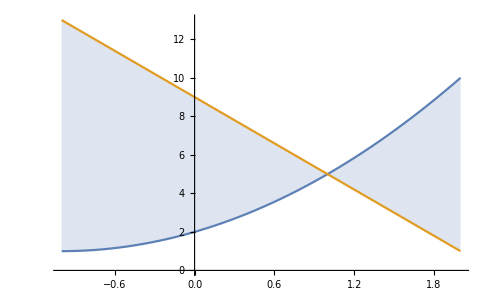
```mathematica
f[x_]:=(x+1)^2+1
g[x_]:=-4x+9
Plot[{f[x],g[x]},{x,-1,2}, Filling-> {1->{2}}]
-Graphics-
Integrate[g[x]-f[x], {x, 0, 1}]
11/3
```

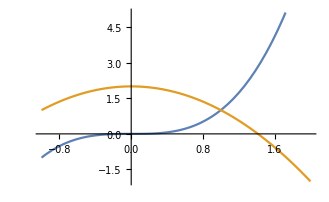
```mathematica
h[x_]:=x^3
j[x_]:=2-x^2
Plot[{h[x],j[x]},{x,-1,2}]
-Graphics-
```

```mathematica
Integrate[h[x], {x, 0, 1}]
```

1/4

```mathematica
N[Integrate[j[x],{x, 1, Sqrt[2]}]]
```

0.218951

```mathematica
N[1/4+0.2189514164974602]
```

0.468951

```mathematica
Integrate[j[x],{x, 1, Sqrt[2]}]
```

1/3-(2 √2)/3+2 (-1+√2)

```mathematica
N[-(2/3)-(3/4) + (2/3)*(2^(3/2))]
```

0.468951